```mathematica
SetDirectory[NotebookDirectory[]];
(*Off[LinearSolve::luc];*)
(*On[LinearSolve::luc]*)
Needs["NDSolve`FEM`"];
Needs["NumericalDifferentialEquationAnalysis`"]
```

```mathematica
ReadABAQUSFile[fileName_:String]:=Module[{nodes,faceElements,lineElements,volumeElements,physicalSurfaceElements,physicalCurveElements,physicalVolumeElements,io,continue,x,p,item,flag,result},
nodes={};
physicalSurfaceElements=<||>;
physicalCurveElements=<||>;
physicalVolumeElements=<||>;
volumeElements=<||>;
faceElements=<||>;
lineElements=<||>;
io=OpenRead[fileName];
continue=True;
While[continue,
x=ReadLine[io];
If[x==EndOfFile,Break[]];
Which[x=="*NODE",flag="NODE";x=ReadLine[io];,
(p=StringPosition[x,"ELSET=Line"])!={},flag="Line"<>StringTake[x,{p[[1,2]]+1,-1}];x=ReadLine[io];lineElements[flag]={};,
(p=StringPosition[x,"ELSET=Surface"])!={},flag="Surface"<>StringTake[x,{p[[1,2]]+1,-1}];x=ReadLine[io];faceElements[flag]={};,
(p=StringPosition[x,"ELSET=Volume"])!={},flag="Volume"<>StringTake[x,{p[[1,2]]+1,-1}];x=ReadLine[io];volumeElements[flag]={};,
(p=StringPosition[x,"ELSET=PhysicalSurface"])!={},flag="PhysicalSurface"<>StringTake[x,{p[[1,2]]+1,-1}];x=ReadLine[io];physicalSurfaceElements[flag]={};,
(p=StringPosition[x,"ELSET=PhysicalCurve"])!={},flag="PhysicalCurve"<>StringTake[x,{p[[1,2]]+1,-1}];x=ReadLine[io];physicalCurveElements[flag]={};,
(p=StringPosition[x,"ELSET=PhysicalVolume"])!={},flag="PhysicalVolume"<>StringTake[x,{p[[1,2]]+1,-1}];x=ReadLine[io];physicalVolumeElements[flag]={};,
x=="******* E L E M E N T S *************",Continue[];
];
Which[flag=="NODE",item=ToExpression[StringReplace[StringSplit[x,", "],{"E"->"*10^","e"->"*10^"}]];AppendTo[nodes,item[[2;;]]];,
StringTake[flag,{1,4}]=="Line",item=ToExpression[StringSplit[x,", "]];AppendTo[lineElements[flag],item[[1;;]]];,
StringTake[flag,{1,7}]=="Surface",item=ToExpression[StringSplit[x,", "]];AppendTo[faceElements[flag],item[[1;;]]];,
StringTake[flag,{1,6}]=="Volume",item=ToExpression[StringSplit[x,", "]];AppendTo[volumeElements[flag],item[[1;;]]];,
StringTake[flag,{1,15}]=="PhysicalSurface",item=ToExpression[StringSplit[x,", "]];AppendTo[physicalSurfaceElements[flag],item[[1;;]]];,
StringTake[flag,{1,14}]=="PhysicalVolume",item=ToExpression[StringSplit[x,", "]];AppendTo[physicalVolumeElements[flag],item[[1;;]]];,
StringTake[flag,{1,13}]=="PhysicalCurve",item=ToExpression[StringSplit[x,", "]];AppendTo[physicalCurveElements[flag],item[[1;;]]];
];
];
Close[io];
result=<||>;
result["nodes"]=nodes;
result["volumeElements"]=volumeElements;
result["faceElements"]=faceElements;
result["lineElements"]=lineElements;
result["physicalSurfaceElements"]=physicalSurfaceElements;
result["physicalVolumeElements"]=physicalVolumeElements;
result["physicalCurveElements"]=physicalCurveElements;
Return[result];
];
```

```mathematica
gauss4={{0.843486716848955000,0.733225086196554000,0.389565010914870000},
{0.748176537037237000,-0.628029428097510000,0.618388506866909000},
{-0.406185150065611000,-0.797379854612102000,0.702412351422850000},
{-0.458109017217254000,0.874301724850955000,0.524343772763987000},
{0.181699364171394000,0.162846601604126000,1.226936695059840000},
{-0.907719697763725000,0.008506794801388040,0.538353662971541000}};
gauss5={{-0.019424272473208600,0.965896490816806000,0.317699958434555000},
{0.019424272473208600,-0.965896490816806000,0.317699958434555000},
{-0.779275100271424000,0.571019834533176000,0.551437495919263000},
{0.779275100271424000,-0.571019834533176000,0.551437495919263000},
{-0.769985051620010000,-0.583486378260079000,0.559433974217610000},
{0.769985051620010000,0.583486378260079000,0.559433974217610000},
{0.000000000000000000,0.000000000000000000,1.142857142857140000}};
gauss6={{-0.734755076167384000,0.893389194164341000,0.218050619143420000},
{0.866215298863403000,-0.703735967051363000,0.268779279771573000},
{0.159687365342462000,-0.908585674928785000,0.317765676342778000},
{-0.890513771429690000,0.164434736850231000,0.348723518701376000},
{-0.146970784674879000,0.535217783554199000,0.715928968895985000},
{0.924000925997766000,0.487964375088803000,0.258691683625119000},
{-0.846332498637550000,-0.839476744821834000,0.194254483173642000},
{-0.408630848287969000,-0.426233087000440000,0.672372076217102000},
{0.517529465272034000,0.917635785070792000,0.262607189133304000},
{0.480100249285706000,-0.100976456182317000,0.742826504995702000}};
gauss7={{0.380554433208316000,-0.380554433208316000,0.520592916667394000},
{-0.380554433208316000,-0.380554433208316000,0.520592916667394000},
{-0.380554433208316000,0.380554433208316000,0.520592916667394000},
{0.380554433208316000,0.380554433208316000,0.520592916667394000},
{-0.805979782918599000,-0.805979782918599000,0.237431774690630000},
{-0.805979782918599000,0.805979782918599000,0.237431774690630000},
{0.805979782918599000,0.805979782918599000,0.237431774690630000},
{0.805979782918599000,-0.805979782918599000,0.237431774690630000},
{-0.925820099772551000,0.000000000000000000,0.241975308641975000},
{0.000000000000000000,0.925820099772551000,0.241975308641975000},
{0.925820099772551000,0.000000000000000000,0.241975308641975000},
{0.000000000000000000,-0.925820099772551000,0.241975308641975000}};
gauss8={{-0.227221864936912000,0.870314604140404000,0.204245745375893000},
{0.278678279812480000,0.985626264019915000,0.073636769118707400},
{0.921572198839564000,0.222409550035862000,0.193156106269186000},
{-0.522942701555180000,-0.928226425988268000,0.160790856417605000},
{0.830917058937661000,0.843511176126523000,0.163511569625457000},
{-0.608025401846290000,0.582594604267371000,0.310286431187124000},
{-0.982254906616708000,-0.821126683194802000,0.064631576881362900},
{0.049594707313616000,-0.691723944678145000,0.429943320894063000},
{0.591001395753786000,-0.261440696978485000,0.456475909576059000},
{0.362658921275484000,0.519812113562016000,0.472513607959160000},
{-0.936916259480118000,0.215377199632934000,0.170104886349013000},
{-0.885013122066316000,0.909038421620713000,0.087048127641865200},
{-0.193465824027229000,0.035263218746432100,0.570953446332848000},
{0.577245368191911000,-0.962255555596149000,0.120349878666210000},
{0.921307016403527000,-0.708268267481712000,0.145235640994558000},
{-0.717603795834097000,-0.413061913973091000,0.377116126710888000}};
gauss9={{-0.927961645959570000,-0.750277099978901000,0.112099602129596000},
{-0.750277099978901000,0.927961645959570000,0.112099602129596000},
{0.927961645959570000,0.750277099978901000,0.112099602129596000},
{0.750277099978901000,-0.927961645959570000,0.112099602129596000},
{-0.630680119731669000,-0.968849966361978000,0.088879378170198700},
{-0.968849966361978000,0.630680119731669000,0.088879378170198700},
{0.630680119731669000,0.968849966361978000,0.088879378170198700},
{0.968849966361978000,-0.630680119731669000,0.088879378170198700},
{-0.852615729333662000,-0.076208328192617200,0.269051337639781000},
{-0.076208328192617200,0.852615729333662000,0.269051337639781000},
{0.852615729333662000,0.076208328192617200,0.269051337639781000},
{0.076208328192617200,-0.852615729333662000,0.269051337639781000},
{-0.453339821135647000,-0.523735820214429000,0.398282439262070000},
{-0.523735820214429000,0.453339821135647000,0.398282439262070000},
{0.453339821135647000,0.523735820214429000,0.398282439262070000},
{0.523735820214429000,-0.453339821135647000,0.398282439262070000},
{0.000000000000000000,0.000000000000000000,0.526748971193416000}};
gauss10={{-0.985383311931460000,0.624024379589848000,0.033387129247072800},
{-0.926210500125839000,-0.957749591600075000,0.034467525588983800},
{-0.911958871035734000,0.206501346198872000,0.134609773861981000},
{-0.879234804399032000,0.922548168257412000,0.062537941187552200},
{0.755126920614355000,-0.953801922342551000,0.071805898760516800},
{-0.318845359683929000,0.940618557199212000,0.119841585323913000},
{-0.647494698175254000,0.647635484262675000,0.230570045533701000},
{0.949219131408870000,0.114295173642238000,0.118617672074660000},
{-0.618866191392992000,-0.107332278651087000,0.314988782212312000},
{-0.921529075578983000,-0.508913190429607000,0.133377311922401000},
{-0.104312325566364000,-0.966342083687359000,0.097940429484131900},
{0.970718373967775000,-0.752965632479960000,0.059110195150351100},
{0.924668424290536000,0.811715106016487000,0.088686202216975400},
{-0.165578525100383000,-0.473248988492766000,0.371717649308962000},
{-0.184471720621220000,0.350726726089190000,0.388114474024409000},
{0.666647330598211000,0.471139214907017000,0.283958422182790000},
{-0.611596783034925000,-0.810374922601918000,0.200183206202775000},
{0.318793575936407000,-0.032110023120386700,0.408241977261546000},
{0.366313916780679000,-0.760506550713974000,0.260423976819169000},
{0.210527389148216000,0.778825415983185000,0.265871134771261000},
{0.763111493924383000,-0.392474875396096000,0.258279394103428000},
{0.625866193532397000,0.981711926404797000,0.063269272761111100}};
gauss11={{-0.953539528201532000,-0.188586138718642000,0.097386777358668200},
{-0.188586138718642000,0.953539528201532000,0.097386777358668200},
{0.953539528201532000,0.188586138718642000,0.097386777358668200},
{0.188586138718642000,-0.953539528201532000,0.097386777358668200},
{-0.698076104549568000,-0.982639223540855000,0.048020763350723800},
{-0.982639223540855000,0.698076104549568000,0.048020763350723800},
{0.698076104549568000,0.982639223540855000,0.048020763350723800},
{0.982639223540855000,-0.698076104549568000,0.048020763350723800},
{-0.939486382816737000,-0.825775835902964000,0.066071329164550600},
{-0.825775835902964000,0.939486382816737000,0.066071329164550600},
{0.939486382816737000,0.825775835902964000,0.066071329164550600},
{0.825775835902964000,-0.939486382816737000,0.066071329164550600},
{-0.712001913075336000,-0.525320250364548000,0.225626061728863000},
{-0.525320250364548000,0.712001913075336000,0.225626061728863000},
{0.712001913075336000,0.525320250364548000,0.225626061728863000},
{0.525320250364548000,-0.712001913075336000,0.225626061728863000},
{-0.315623432915254000,-0.812520548304813000,0.211736349998949000},
{-0.812520548304813000,0.315623432915254000,0.211736349998949000},
{0.315623432915254000,0.812520548304813000,0.211736349998949000},
{0.812520548304813000,-0.315623432915254000,0.211736349998949000},
{-0.424847248848669000,-0.041658071912022400,0.351158718398245000},
{-0.041658071912022400,0.424847248848669000,0.351158718398245000},
{0.424847248848669000,0.041658071912022400,0.351158718398245000},
{0.041658071912022400,-0.424847248848669000,0.351158718398245000}};
gauss12={{0.971118510791888000,-0.867210515421397000,0.032446573473288600},
{0.648945077104548000,0.992892264470200000,0.032098668836952100},
{-0.954754310426266000,0.285749318138334000,0.053938113558348900},
{-0.906577798800004000,0.965601179017672000,0.027175061499162300},
{0.928804579128737000,0.892120795107226000,0.048562101347638000},
{-0.942516235813952000,-0.910021954360750000,0.035406095224694000},
{-0.943810852314883000,0.700039350143640000,0.058716829387645600},
{-0.647728588508900000,-0.966463450777580000,0.047867553179783400},
{0.939998303704761000,0.476900667530568000,0.084294348992589200},
{-0.686628278265943000,0.425746709473961000,0.180127205439828000},
{0.737991350126812000,-0.961515356209681000,0.051332164430571100},
{-0.329315228881971000,0.969360425311981000,0.060646455914650200},
{0.655639958261631000,0.711304224974728000,0.167844019822143000},
{0.425730911187153000,-0.794328546102697000,0.173090937578105000},
{0.969282947689749000,-0.199284039825590000,0.067542452621593500},
{-0.850572109762236000,-0.079907732090007900,0.146739833220569000},
{0.207926438217394000,0.887670466574004000,0.143874300374211000},
{-0.802520178290368000,-0.664976089105782000,0.133527391811298000},
{-0.519723746635557000,-0.339077954204338000,0.235175559489683000},
{-0.002734035281447750,-0.535447139041843000,0.247792631850410000},
{-0.369965842884512000,0.150282009936021000,0.217139027539975000},
{-0.655897074460724000,0.833402904613771000,0.117824501522532000},
{0.320273497814413000,0.388155910514854000,0.275978368559438000},
{0.824446949855471000,-0.587985692223445000,0.149281018226312000},
{0.022789251235421000,-0.020009917527598100,0.247426924349583000},
{0.056518969343591500,-0.964672163792294000,0.072569402619307000},
{0.488996833895482000,-0.276164203985181000,0.255169564837882000},
{-0.355597615682237000,-0.812829416253859000,0.159456865509374000},
{0.757551296706625000,0.121534454639901000,0.198033456224445000},
{-0.187023431511228000,0.639027422929934000,0.243423165673119000},
{-0.996774104263165000,-0.440003600454197000,0.035499406884868900}};
gauss13={{-0.957297699786307000,-0.859556005641639000,0.038174421317083700},
{-0.859556005641639000,0.957297699786307000,0.038174421317083700},
{0.957297699786307000,0.859556005641639000,0.038174421317083700},
{0.859556005641639000,-0.957297699786307000,0.038174421317083700},
{-0.778809711554419000,-0.983486682439872000,0.029991838864499100},
{-0.983486682439872000,0.778809711554419000,0.029991838864499100},
{0.778809711554419000,0.983486682439872000,0.029991838864499100},
{0.983486682439872000,-0.778809711554419000,0.029991838864499100},
{-0.475808625218276000,-0.850076673699749000,0.118844667300596000},
{-0.850076673699749000,0.475808625218276000,0.118844667300596000},
{0.475808625218276000,0.850076673699749000,0.118844667300596000},
{0.850076673699749000,-0.475808625218276000,0.118844667300596000},
{-0.941327225872925000,-0.390736216129461000,0.077492738533105300},
{-0.390736216129461000,0.941327225872925000,0.077492738533105300},
{0.941327225872925000,0.390736216129461000,0.077492738533105300},
{0.390736216129461000,-0.941327225872925000,0.077492738533105300},
{-0.138183459862465000,-0.958925170287535000,0.060424923817750000},
{-0.958925170287535000,0.138183459862465000,0.060424923817750000},
{0.138183459862465000,0.958925170287535000,0.060424923817750000},
{0.958925170287535000,-0.138183459862465000,0.060424923817750000},
{-0.755805356572081000,-0.647821637187011000,0.129763550370003000},
{-0.647821637187011000,0.755805356572081000,0.129763550370003000},
{0.755805356572081000,0.647821637187011000,0.129763550370003000},
{0.647821637187011000,-0.755805356572081000,0.129763550370003000},
{-0.696250078491749000,-0.070741508996444900,0.213341581457189000},
{-0.070741508996444900,0.696250078491749000,0.213341581457189000},
{0.696250078491749000,0.070741508996444900,0.213341581457189000},
{0.070741508996444900,-0.696250078491749000,0.213341581457189000},
{-0.342716556040407000,-0.409304561694039000,0.256870749481968000},
{-0.409304561694039000,0.342716556040407000,0.256870749481968000},
{0.342716556040407000,0.409304561694039000,0.256870749481968000},
{0.409304561694039000,-0.342716556040407000,0.256870749481968000},
{0.000000000000000000,0.000000000000000000,0.300382115431225000}};
gauss14={{0.987428065667973000,0.941534257799352000,0.009363772347063210},
{0.823749537546361000,-0.978335523037781000,0.025686318842409200},
{0.124628394327203000,-0.982817268459149000,0.038820415167070200},
{-0.933002196549752000,0.949122163506687000,0.024171748002861500},
{-0.912505468462708000,-0.953265951862068000,0.026848018653344100},
{-0.549088414869222000,0.976652434660452000,0.040046201264013300},
{0.785699586088601000,0.962240606035239000,0.035636834322279300},
{0.212910618139605000,0.980090430119475000,0.043715334341660100},
{0.973411200385749000,-0.870658415382593000,0.024541150793432300},
{-0.530131098403591000,-0.962347290628517000,0.051589965754795900},
{-0.995578713598433000,-0.755839032835375000,0.017249010205808100},
{-0.975408156677302000,0.656653809710659000,0.035715402909703000},
{0.919467586286639000,0.756319724568914000,0.054859489530845000},
{0.713657387041791000,-0.762357855489723000,0.073421187062028600},
{0.972680527200081000,-0.300116438582365000,0.045522626832604600},
{0.485379015395184000,-0.898013872622527000,0.085614380771066100},
{0.967737633871251000,0.338930020129301000,0.052550964814311100},
{-0.763097308948618000,0.814045140152194000,0.088403294862707800},
{-0.658882431645275000,0.221098201889707000,0.097309244660748500},
{0.878569444190056000,-0.603445470435037000,0.078331363527017000},
{0.522360556081928000,0.844295767450015000,0.110286386231653000},
{-0.963671352206945000,0.023104886405496800,0.060233904113805300},
{-0.757520436906965000,-0.782240390955490000,0.096688944690637100},
{-0.915768975432255000,-0.468622830364355000,0.077665642197365900},
{-0.177414179137809000,0.870134831103716000,0.126901606044106000},
{-0.174184096048568000,-0.841607946331074000,0.134041788424363000},
{0.749799339156942000,0.559342841512316000,0.113541249163745000},
{-0.847741827517617000,0.394776494566506000,0.106695809121560000},
{-0.735474719020045000,-0.219802335337856000,0.140779315332983000},
{-0.419635246005996000,0.005707664645153700,0.172637156229719000},
{0.512148817551407000,0.310132758071037000,0.180772164902436000},
{-0.473805498592473000,0.608667036314688000,0.173517815735895000},
{0.184133342257543000,0.638360320212070000,0.187032886731351000},
{-0.471728128885813000,-0.566223245535039000,0.175288518977746000},
{0.820134523164239000,0.008081675629410630,0.146573351434251000},
{0.223473028337477000,-0.638479693447521000,0.192066348467456000},
{0.582793993815248000,-0.357622214112894000,0.195817764047422000},
{-0.106022540532044000,-0.317733518368168000,0.216558741836653000},
{-0.114468533485019000,0.320467412131102000,0.219911862198891000},
{0.250081578248540000,-0.023679786372971800,0.223592019452193000}};
gauss15={{0.903395953817165000,-0.640607269699869000,0.066405048827649100},
{-0.903395953817165000,0.640607269699869000,0.066405048827649100},
{-0.550134294936478000,0.115183488397160000,0.156674604555739000},
{0.550134294936478000,-0.115183488397160000,0.156674604555739000},
{-0.779192318831319000,-0.959803102531884000,0.036417393946004000},
{0.779192318831319000,0.959803102531884000,0.036417393946004000},
{-0.900007562424909000,-0.739786564246218000,0.067691043974839100},
{0.900007562424909000,0.739786564246218000,0.067691043974839100},
{0.528533088048687000,0.827469885439658000,0.108349391272857000},
{-0.528533088048687000,-0.827469885439658000,0.108349391272857000},
{-0.983935675037342000,-0.938106220953278000,0.011316840315755700},
{0.983935675037342000,0.938106220953278000,0.011316840315755700},
{-0.903719453119829000,0.969668784857443000,0.019462515095628400},
{0.903719453119829000,-0.969668784857443000,0.019462515095628400},
{-0.978776967339373000,-0.402472204888805000,0.037641248550359600},
{0.978776967339373000,0.402472204888805000,0.037641248550359600},
{-0.278640687603701000,-0.977212602358721000,0.040874537477459700},
{0.278640687603701000,0.977212602358721000,0.040874537477459700},
{-0.691766919281190000,-0.492216324503046000,0.144480172165797000},
{0.691766919281190000,0.492216324503046000,0.144480172165797000},
{0.732048720266706000,-0.412057567150867000,0.119866554458781000},
{-0.732048720266706000,0.412057567150867000,0.119866554458781000},
{0.852261793437990000,0.098401891739229900,0.119723911438850000},
{-0.852261793437990000,-0.098401891739229900,0.119723911438850000},
{-0.183489520295498000,-0.631330653651061000,0.173979010536173000},
{0.183489520295498000,0.631330653651061000,0.173979010536173000},
{0.374284045054871000,0.249040991081743000,0.183605676270157000},
{-0.374284045054871000,-0.249040991081743000,0.183605676270157000},
{0.446809246621294000,-0.982420210898417000,0.033904810152218000},
{-0.446809246621294000,0.982420210898417000,0.033904810152218000},
{-0.186387418592140000,0.374475204235935000,0.189902529172520000},
{0.186387418592140000,-0.374475204235935000,0.189902529172520000},
{-0.713920141620587000,0.865369521592895000,0.076485128312616300},
{0.713920141620587000,-0.865369521592895000,0.076485128312616300},
{0.097987746324254600,-0.880515371033278000,0.110527300751247000},
{-0.097987746324254600,0.880515371033278000,0.110527300751247000},
{-0.438023389008309000,0.677578059813511000,0.146622000894122000},
{0.438023389008309000,-0.677578059813511000,0.146622000894122000},
{0.993054873675666000,-0.836999252036426000,0.013354920743425000},
{-0.993054873675666000,0.836999252036426000,0.013354920743425000},
{-0.969541800001706000,0.246721181968066000,0.048013596267850500},
{0.969541800001706000,-0.246721181968066000,0.048013596267850500},
{0.000000000000000000,0.000000000000000000,0.189403529639906000}};
gauss16={{0.445507731511760000,-0.413354471860305000,0.109750895772137000},
{-0.284863997843656000,-0.773904595707985000,0.092735422633705600},
{0.328161273106660000,-0.941861837644287000,0.049391484580315100},
{0.891832309089729000,-0.560635547357923000,0.069330331777409700},
{0.508073945520771000,0.969871742373536000,0.029299402386489900},
{-0.160401483833674000,-0.489219773124481000,0.136663297243251000},
{-0.508478601397568000,-0.911705004489780000,0.060463687877800200},
{0.683050166161883000,-0.514627868662472000,0.060123196563886000},
{0.039586090785457300,-0.881060036231116000,0.065253710411357500},
{-0.950588422848696000,-0.954571119120115000,0.014266646693945500},
{-0.961811711954693000,-0.546625841304211000,0.036739985227339600},
{-0.982487660585620000,-0.803832199075330000,0.010244450090046800},
{0.729490988437544000,-0.173843852523866000,0.122891309996644000},
{0.166351217681414000,-0.652112340518726000,0.109894199726909000},
{-0.840134640602696000,-0.319976277566376000,0.096517045365247200},
{0.719682815977335000,0.858335244426420000,0.069902607889499200},
{0.253027222625072000,0.955971316096198000,0.027426590492737200},
{0.064031285585747200,0.863844202235313000,0.088921001652764700},
{0.986764924506288000,-0.778264694557827000,0.017375896748023900},
{-0.200957026759874000,0.657732191273258000,0.145651931566765000},
{-0.438568504540564000,-0.242952497473152000,0.159671762122283000},
{0.994272049902797000,0.387605436167795000,0.020779665435939400},
{-0.830657768685456000,-0.795121712804385000,0.062664700993627900},
{0.154009336884112000,-0.216310560329634000,0.167317474426306000},
{0.512723039736232000,-0.752259893090806000,0.089881496004709700},
{-0.989669701921178000,0.591442252708451000,0.021603558022165100},
{0.972167735595001000,-0.239092772057367000,0.040181048915884200},
{-0.743218986355082000,-0.974999448316560000,0.020823333907520300},
{0.784520617659537000,-0.844462201482182000,0.058394486724204400},
{0.979238292497834000,0.881077515951339000,0.016252892003197900},
{-0.707147287315070000,0.617318772716463000,0.111484205211110000},
{-0.141689189603232000,0.072923246521249000,0.189466157687559000},
{0.890111884447047000,0.138973166621706000,0.087905584926457000},
{0.899129162264493000,0.653912166307646000,0.067064255945613800},
{-0.894878758684030000,0.815240964820200000,0.049925668679124900},
{-0.168523642369061000,-0.993958227705161000,0.023528131123758600},
{0.881461425914387000,0.981867680867930000,0.015197244781246200},
{-0.972779448110078000,0.958201000795796000,0.009821024046902650},
{-0.233564065275655000,0.982416285210725000,0.032509307669707700},
{0.931748401454671000,-0.961120359879646000,0.017406856905030000},
{0.446254832379450000,0.101479668111595000,0.179297928216825000},
{-0.495660944887794000,0.863008322414298000,0.089033333438222300},
{-0.746446232595771000,0.969355393612973000,0.029218615831767100},
{-0.620928875744261000,-0.596902749809026000,0.122372159668821000},
{-0.972990462530664000,-0.037898803254192100,0.041556480444634500},
{0.685168921146318000,0.427270495865275000,0.135770957895265000},
{-0.695023798277837000,0.043133028575848300,0.136084263048921000},
{0.140697364739904000,0.410194195219477000,0.185021861982314000},
{-0.890351974415560000,0.327795012881707000,0.086484301880239100},
{-0.449445901363072000,0.354026690962790000,0.161837684628526000},
{0.639385538397514000,-0.978631148237155000,0.023026899599951600},
{0.418560468778428000,0.696096846616176000,0.135573563135892000}};
gauss17={{0.964887903404074000,0.985689382234412000,0.006193712147584860},
{-0.964887903404074000,-0.985689382234412000,0.006193712147584860},
{-0.330286592219223000,0.949849271029669000,0.043236496307830300},
{0.330286592219223000,-0.949849271029669000,0.043236496307830300},
{-0.888198789160951000,0.872196235222607000,0.040255887203418500},
{0.888198789160951000,-0.872196235222607000,0.040255887203418500},
{-0.814329626204568000,-0.612412291293688000,0.084738850372002100},
{0.814329626204568000,0.612412291293688000,0.084738850372002100},
{-0.796096362345474000,-0.931225803270203000,0.041280861876464100},
{0.796096362345474000,0.931225803270203000,0.041280861876464100},
{-0.984861648020128000,0.093840166632710700,0.026583778860236800},
{0.984861648020128000,-0.093840166632710700,0.026583778860236800},
{-0.140894433326407000,0.715271677314684000,0.128804581631980000},
{0.140894433326407000,-0.715271677314684000,0.128804581631980000},
{-0.203358761087873000,-0.892410578937601000,0.074538835076491200},
{0.203358761087873000,0.892410578937601000,0.074538835076491200},
{0.907497621392903000,-0.398635702010268000,0.070078380263111300},
{-0.907497621392903000,0.398635702010268000,0.070078380263111300},
{-0.333830471920583000,-0.032196823216938500,0.181919891554460000},
{0.333830471920583000,0.032196823216938500,0.181919891554460000},
{-0.037993248927978300,0.883128912942483000,0.016938077789591700},
{0.037993248927978300,-0.883128912942483000,0.016938077789591700},
{-0.539526254022450000,0.831100894169927000,0.076673869693328600},
{0.539526254022450000,-0.831100894169927000,0.076673869693328600},
{-0.493849631097933000,-0.982837463363535000,0.025152925390091900},
{0.493849631097933000,0.982837463363535000,0.025152925390091900},
{-0.558836165383315000,-0.783645040768903000,0.095495102971246200},
{0.558836165383315000,0.783645040768903000,0.095495102971246200},
{-0.717411836909067000,0.977154483938849000,0.024036354754529700},
{0.717411836909067000,-0.977154483938849000,0.024036354754529700},
{0.429595537049770000,-0.467677367688358000,0.152745088597566000},
{-0.429595537049770000,0.467677367688358000,0.152745088597566000},
{0.983378332468192000,-0.689377160866396000,0.021357813628790400},
{-0.983378332468192000,0.689377160866396000,0.021357813628790400},
{0.024180495276639400,-0.990986935183992000,0.016126984571367200},
{-0.024180495276639400,0.990986935183992000,0.016126984571367200},
{0.683224740971240000,-0.174667814835351000,0.138109330474059000},
{-0.683224740971240000,0.174667814835351000,0.138109330474059000},
{0.031193074088170000,-0.277141221673766000,0.185474034022693000},
{-0.031193074088170000,0.277141221673766000,0.185474034022693000},
{0.748197697295448000,-0.645027227063472000,0.089124842737353800},
{-0.748197697295448000,0.645027227063472000,0.089124842737353800},
{0.971427244621435000,0.434884203591433000,0.034970676318000700},
{-0.971427244621435000,-0.434884203591433000,0.034970676318000700},
{-0.268953347046064000,-0.562711843706795000,0.153244772454862000},
{0.268953347046064000,0.562711843706795000,0.153244772454862000},
{-0.599115140753120000,-0.341655819406524000,0.144376263400463000},
{0.599115140753120000,0.341655819406524000,0.144376263400463000},
{-0.865728982855016000,-0.140812489244356000,0.092019656065567400},
{0.865728982855016000,0.140812489244356000,0.092019656065567400},
{-0.957652829326075000,-0.808324607852891000,0.029979234047981000},
{0.957652829326075000,0.808324607852891000,0.029979234047981000},
{0.975228555177618000,-0.974579651207927000,0.006543697788929640},
{-0.975228555177618000,0.974579651207927000,0.006543697788929640}};
gauss18={{-0.982429297281976000,-0.949230454013695000,0.006901620813203700},
{-0.980380015083047000,0.946960902613153000,0.008204870814717420},
{0.978687397095401000,0.762218621925671000,0.019278596336483400},
{0.978306471706846000,-0.919698374876273000,0.010969327077447300},
{0.972103651465078000,0.976418347003238000,0.006009552531394270},
{0.593429919248951000,-0.961646672052616000,0.034637323795903300},
{0.597634101219750000,0.834358971111738000,0.038907120558780900},
{-0.369296188601143000,0.980003693855253000,0.026378796938873700},
{0.704947905579518000,0.987074733006691000,0.016416586385974900},
{-0.737346800800434000,-0.833346048241695000,0.041145861713737800},
{0.986198906466038000,-0.327873774089739000,0.022825540585567400},
{-0.084651582098743200,0.890846684308923000,0.073103135101909100},
{0.885013997448202000,-0.985580362683214000,0.010449045745085100},
{-0.931392615028488000,-0.821284513547405000,0.028591162230098100},
{-0.708998195731981000,0.682214391217305000,0.065563219850278700},
{0.873261409217360000,0.903114876131973000,0.032746370301029400},
{-0.841939921562292000,0.988578670736746000,0.011052740997420800},
{0.322427946202822000,0.053651543933953500,0.053304519431588300},
{0.224464012452270000,0.735043760027014000,0.111454315838592000},
{-0.834718000493207000,0.508460910847036000,0.056410943648423900},
{-0.827953630478415000,-0.613231512811576000,0.057697163188087800},
{-0.656812538100131000,0.229078070335026000,0.093984010825691900},
{-0.846004296423096000,-0.978641815587594000,0.015168101019882500},
{-0.924217429470286000,-0.310257784576101000,0.054707804999563400},
{-0.541436884489988000,-0.627509839174689000,0.078099963413585800},
{0.926530484170682000,0.014074835774001700,0.046018476274623400},
{-0.898115617304339000,0.829568002296710000,0.038928835116846500},
{-0.411573212027108000,0.775319650278541000,0.086519386166870300},
{0.604745362251865000,-0.652631659900920000,0.101381855266143000},
{-0.598390083509815000,-0.933367462258878000,0.037058378130401900},
{0.432039779064828000,0.924343278338674000,0.047980615285732800},
{0.449966723415258000,0.070056469899358400,0.105475282654227000},
{0.951376456460360000,-0.692596950625775000,0.035049058915163800},
{-0.679597970094767000,-0.364194575899888000,0.091181315541955200},
{-0.656465211852405000,0.919366501804594000,0.046451973042803000},
{0.837804785251729000,-0.463991552565486000,0.075926009285387200},
{-0.111355677239084000,-0.904193692071085000,0.064283617076494100},
{-0.360874696271078000,-0.780886581875027000,0.076325340231549200},
{0.986275390417332000,0.297446798275277000,0.021492114487638500},
{-0.233191897888659000,-0.434374605151552000,0.145899258412579000},
{-0.987049222797420000,-0.589832299076629000,0.017414852375781700},
{-0.989416085475088000,-0.016043833664557500,0.019087391986355000},
{-0.983650223879544000,0.639347783923839000,0.019733044490481700},
{0.800243244261134000,-0.848162973199419000,0.053086763935160700},
{0.649240423985066000,-0.205450771719314000,0.116789037510446000},
{0.870116072569919000,-0.101735576456373000,0.035201523921065800},
{0.738932138510633000,0.715956827979010000,0.064296573796207800},
{-0.471585503056962000,-0.124581708848908000,0.133675188464838000},
{0.743616535820214000,0.254253207680442000,0.110904939025308000},
{0.353483468476925000,-0.841519989806880000,0.083112287466240600},
{-0.365084945207516000,-0.989721938369978000,0.017663540854226700},
{-0.228350620871312000,0.155638454565645000,0.153997017629200000},
{0.174027410246762000,-0.979107432403171000,0.027596486130759100},
{0.899583978350057000,0.529526741134148000,0.059105433701516100},
{0.340592565502600000,-0.416539106933105000,0.146126955531040000},
{0.042953287922524400,-0.150980236568745000,0.164383243522768000},
{0.144865301606391000,0.334737666273857000,0.144789829840957000},
{-0.131282782124110000,0.575950475129962000,0.124514097254645000},
{0.500463829568670000,0.508698598301963000,0.126014121327927000},
{0.060066092592200400,-0.666195176990418000,0.125502053787605000},
{0.155225723288537000,0.984726449650269000,0.022665912773319600},
{-0.939586463235499000,0.300334253456423000,0.047781667991276900},
{-0.479150775895990000,0.449232669783580000,0.107412813357199000},
{-0.813790239732564000,-0.006261874651131660,0.085166013293940000}};
gauss19={{0.989550293378263000,-0.922241297939262000,0.007454074183434390},
{-0.989550293378263000,0.922241297939262000,0.007454074183434390},
{0.985042240162801000,-0.537975757267246000,0.019492449141150700},
{-0.985042240162801000,0.537975757267246000,0.019492449141150700},
{0.542794079863946000,-0.984763200222394000,0.019576503674580500},
{-0.542794079863946000,0.984763200222394000,0.019576503674580500},
{-0.982058311616186000,-0.979457233373964000,0.004115071951785320},
{0.982058311616186000,0.979457233373964000,0.004115071951785320},
{0.980375162387800000,-0.023558419803885700,0.026736583720974200},
{-0.980375162387800000,0.023558419803885700,0.026736583720974200},
{0.894758184772389000,-0.980993759673845000,0.011484151125267100},
{-0.894758184772389000,0.980993759673845000,0.011484151125267100},
{-0.267067791810323000,0.916721096671647000,0.060418311456532600},
{0.267067791810323000,-0.916721096671647000,0.060418311456532600},
{-0.919996866636276000,0.771805990475130000,0.039085118826832100},
{0.919996866636276000,-0.771805990475130000,0.039085118826832100},
{0.139767717177689000,0.496876315708040000,0.084558781311823700},
{-0.139767717177689000,-0.496876315708040000,0.084558781311823700},
{-0.800342433371430000,-0.972769023962788000,0.018751190844663700},
{0.800342433371430000,0.972769023962788000,0.018751190844663700},
{-0.926385097050591000,-0.875739874597839000,0.026349915003489500},
{0.926385097050591000,0.875739874597839000,0.026349915003489500},
{0.955556767367176000,0.390024695408791000,0.040159812749493900},
{-0.955556767367176000,-0.390024695408791000,0.040159812749493900},
{0.426482853817253000,0.661837040055220000,0.104367666379410000},
{-0.426482853817253000,-0.661837040055220000,0.104367666379410000},
{-0.511280057692590000,0.757160427482759000,0.088431537963157000},
{0.511280057692590000,-0.757160427482759000,0.088431537963157000},
{0.448835747568207000,0.115897428347129000,0.124189438269148000},
{-0.448835747568207000,-0.115897428347129000,0.124189438269148000},
{0.018167889129269200,0.290451324614677000,0.061735469393431000},
{-0.018167889129269200,-0.290451324614677000,0.061735469393431000},
{-0.900035919932745000,0.301856827917365000,0.064310564995541700},
{0.900035919932745000,-0.301856827917365000,0.064310564995541700},
{0.842536976481717000,0.638431501025987000,0.064984805782746300},
{-0.842536976481717000,-0.638431501025987000,0.064984805782746300},
{0.741584296568994000,-0.897956344126679000,0.045618800003863200},
{-0.741584296568994000,0.897956344126679000,0.045618800003863200},
{-0.228488601509752000,-0.878000817487651000,0.067399464211402300},
{0.228488601509752000,0.878000817487651000,0.067399464211402300},
{-0.533759454128371000,0.377012996246757000,0.100098042479357000},
{0.533759454128371000,-0.377012996246757000,0.100098042479357000},
{-0.838523574984381000,-0.148606808511603000,0.078942921097676700},
{0.838523574984381000,0.148606808511603000,0.078942921097676700},
{0.764991114385795000,-0.579925083943397000,0.082725936061673800},
{-0.764991114385795000,0.579925083943397000,0.082725936061673800},
{-0.990519649910825000,-0.707893130646025000,0.012498294037940800},
{0.990519649910825000,0.707893130646025000,0.012498294037940800},
{-0.480114415232144000,-0.966919239598312000,0.031308072045425300},
{0.480114415232144000,0.966919239598312000,0.031308072045425300},
{-0.269983299972902000,-0.327468449127939000,0.066931086517704400},
{0.269983299972902000,0.327468449127939000,0.066931086517704400},
{-0.666259933104086000,-0.832876882576045000,0.064391231036940300},
{0.666259933104086000,0.832876882576045000,0.064391231036940300},
{-0.039869923253439600,0.743290514481814000,0.091748719336349900},
{0.039869923253439600,-0.743290514481814000,0.091748719336349900},
{-0.690765194121908000,0.119769775111669000,0.095572972754816600},
{0.690765194121908000,-0.119769775111669000,0.095572972754816600},
{-0.651687204457113000,-0.414885613004337000,0.108752778744985000},
{0.651687204457113000,0.414885613004337000,0.108752778744985000},
{0.247249943393367000,-0.173945322711955000,0.111738119026117000},
{-0.247249943393367000,0.173945322711955000,0.111738119026117000},
{0.026921939590956200,0.987202373974218000,0.021698973567425600},
{-0.026921939590956200,-0.987202373974218000,0.021698973567425600},
{0.263926275357656000,-0.540311728085682000,0.105622908847031000},
{-0.263926275357656000,0.540311728085682000,0.105622908847031000},
{0.000000000000000000,0.000000000000000000,0.097500466915658900}};
gauss20={{0.790355590129828000,-0.088982481688452000,0.059691281598230600},
{0.225227378936248000,-0.072809539044851700,0.059545020382775500},
{-0.137155620335222000,-0.865352420156083000,0.058145321847650000},
{0.951691246765190000,-0.290234658519754000,0.022665923467031700},
{0.898143861379741000,0.121866004809799000,0.051194065051477000},
{0.351132733693233000,-0.247122128270212000,0.080889636133250000},
{0.097590683430625400,-0.746791529620094000,0.078544461522525700},
{-0.192078170221083000,-0.558983078908140000,0.099390188730238300},
{0.669543630688509000,-0.209065194159909000,0.054832228471298500},
{0.583028950570240000,-0.435570440609949000,0.079417687672137900},
{-0.427819022720551000,-0.726477160564427000,0.079647757987957000},
{0.057278453165736000,-0.136359038895054000,0.026582651674851300},
{0.735150720092603000,-0.987851280266917000,0.001856943247818100},
{0.789893496423454000,0.920973773207876000,0.029828900971153200},
{-0.359439977748291000,-0.953521739150114000,0.034669167330477800},
{0.337683918311246000,-0.595336123802651000,0.092721810004885000},
{0.988639671491411000,-0.075158637054292400,0.015828377299189800},
{-0.390772159666108000,0.986549145205441000,0.010062925779008200},
{-0.604689913975449000,-0.994093902917823000,0.009495171620836120},
{0.917300715303028000,-0.984083290419238000,0.008323819832226610},
{-0.041413969036599300,0.082848985642712800,0.117508185028318000},
{-0.638598289581018000,-0.866072058466825000,0.050782546480554200},
{0.601339613443807000,0.980945003785699000,0.017622906439958200},
{0.916166166199854000,0.804853349912937000,0.028551259360018900},
{-0.327863985922172000,0.279028974015123000,0.119526726306184000},
{0.880246022798184000,-0.408274384303883000,0.045943455672117800},
{-0.203458107806014000,0.974022665495887000,0.018971829504327600},
{0.696916639983928000,0.303569758201840000,0.091541128358184700},
{0.535159329380387000,-0.986272598512079000,0.016196100112054600},
{-0.278774781983711000,0.718567295217056000,0.083052698265834200},
{0.991031447937170000,-0.919325614569451000,0.006376631911871850},
{-0.825288926425955000,-0.954438424512673000,0.021119911143429100},
{-0.959949120689160000,-0.989814634983996000,0.003768904506335160},
{0.494491683571411000,0.073389471362591100,0.108962414915352000},
{-0.770389671618066000,-0.207533046378098000,0.080991365260831300},
{0.912960483771139000,0.990731899896839000,0.006403846513639610},
{0.850037386649928000,0.538798622046948000,0.060525756735492300},
{-0.037554533546959200,0.883413145142967000,0.060605862620850700},
{-0.973457410521752000,-0.893452263890975000,0.011415694760965500},
{0.289701677031343000,-0.920765697224696000,0.052344618138453500},
{0.768843829066036000,-0.636707611475453000,0.065242312488914900},
{-0.838861851699083000,0.997891319631791000,0.005609045829389010},
{-0.534128691368410000,0.530094394935641000,0.096009334952416800},
{-0.917480683143074000,-0.426299825967388000,0.049227547705821000},
{-0.947434683884687000,0.184114456716033000,0.027703703053861200},
{-0.061319362631778400,0.509069104271246000,0.113050454590628000},
{0.760593310631716000,-0.921450161258118000,0.034412967828469200},
{-0.984888646257559000,-0.640002781164244000,0.015032949378809800},
{-0.757298782045933000,0.320923167891418000,0.087264900853697000},
{0.050807456822810600,-0.384663640517674000,0.106376878833305000},
{-0.463655002935500000,0.869716109569750000,0.051216366817071500},
{0.970531924422749000,0.347009842836962000,0.026008005827600700},
{-0.891407994726378000,0.571123931193509000,0.051417985692617800},
{-0.987305695483006000,0.406791291429793000,0.015380449168071900},
{-0.975831337288964000,0.762478652445822000,0.017473005130117700},
{-0.881917086918621000,-0.777014374525921000,0.037769069336539500},
{-0.970963589527841000,0.958435680255076000,0.008140560550227890},
{0.982272226270234000,0.655197397645968000,0.014374212737193300},
{-0.887350394289104000,0.028545787727207300,0.044623465511291600},
{-0.656924708204403000,0.955161978068076000,0.026073785474301800},
{-0.987090537362271000,-0.167518567702980000,0.019273559493088100},
{-0.573467455165415000,0.042400212843295100,0.113856098790220000},
{0.015078886190834000,-0.986454503960649000,0.019995333543228000},
{0.550605056055349000,-0.798955027886182000,0.070983819569712000},
{-0.736683988577231000,-0.607183999696622000,0.072072790057625400},
{-0.711702655633243000,0.738867205408202000,0.063524900182586100},
{0.233396592239589000,0.314077512069275000,0.121934711408448000},
{-0.287868115247493000,-0.179382635380280000,0.127739827178937000},
{0.436174699035284000,0.877233698204943000,0.059601000096145100},
{0.981463389559936000,-0.603307689849467000,0.018606358989187200},
{-0.531960163499168000,-0.403980518928954000,0.103355984699723000},
{0.985098752202256000,0.928249862549075000,0.007243885756143160},
{0.195797282497072000,0.718509878376443000,0.094080114226498900},
{0.208421740019590000,0.975809076098629000,0.026709615274027100},
{0.475502772074220000,0.538825545534923000,0.101301034994317000},
{0.914749484368615000,-0.802021243175542000,0.033262308047398600},
{-0.864568932816552000,0.881433597644919000,0.030653291281114500},
{0.677221207092729000,0.739326748786804000,0.067853181991462500}};
gauss21={{-0.977261191379831000,-0.981979368177324000,0.003553851441571220},
{-0.981979368177324000,0.977261191379831000,0.003553851441571220},
{0.977261191379831000,0.981979368177324000,0.003553851441571220},
{0.981979368177324000,-0.977261191379831000,0.003553851441571220},
{-0.727163296191593000,-0.999176915515979000,0.007309639483174840},
{-0.999176915515979000,0.727163296191593000,0.007309639483174840},
{0.727163296191593000,0.999176915515979000,0.007309639483174840},
{0.999176915515979000,-0.727163296191593000,0.007309639483174840},
{0.472936439935032000,-0.992247874111186000,0.012547114287276200},
{-0.992247874111186000,-0.472936439935032000,0.012547114287276200},
{-0.472936439935032000,0.992247874111186000,0.012547114287276200},
{0.992247874111186000,0.472936439935032000,0.012547114287276200},
{0.836573759741210000,-0.978569524191080000,0.012832695725929300},
{-0.978569524191080000,-0.836573759741210000,0.012832695725929300},
{-0.836573759741210000,0.978569524191080000,0.012832695725929300},
{0.978569524191080000,0.836573759741210000,0.012832695725929300},
{-0.884476674464786000,-0.941438812300101000,0.019120137325233500},
{-0.941438812300101000,0.884476674464786000,0.019120137325233500},
{0.884476674464786000,0.941438812300101000,0.019120137325233500},
{0.941438812300101000,-0.884476674464786000,0.019120137325233500},
{-0.021383321768837200,-0.986536782114746000,0.015648429419403300},
{-0.986536782114746000,0.021383321768837200,0.015648429419403300},
{0.021383321768837200,0.986536782114746000,0.015648429419403300},
{0.986536782114746000,-0.021383321768837200,0.015648429419403300},
{-0.651043209177119000,0.924125418800791000,0.034851588124248900},
{0.924125418800791000,0.651043209177119000,0.034851588124248900},
{0.651043209177119000,-0.924125418800791000,0.034851588124248900},
{-0.924125418800791000,-0.651043209177119000,0.034851588124248900},
{-0.968191519508536000,0.369723730149738000,0.027535412298343500},
{0.369723730149738000,0.968191519508536000,0.027535412298343500},
{0.968191519508536000,-0.369723730149738000,0.027535412298343500},
{-0.369723730149738000,-0.968191519508536000,0.027535412298343500},
{-0.237861893972090000,-0.194835467763778000,0.093318944129379000},
{-0.194835467763778000,0.237861893972090000,0.093318944129379000},
{0.237861893972090000,0.194835467763778000,0.093318944129379000},
{0.194835467763778000,-0.237861893972090000,0.093318944129379000},
{-0.112426962821608000,0.705609457571060000,0.092401997861655900},
{0.705609457571060000,0.112426962821608000,0.092401997861655900},
{0.112426962821608000,-0.705609457571060000,0.092401997861655900},
{-0.705609457571060000,-0.112426962821608000,0.092401997861655900},
{0.257883724388743000,0.594205876515535000,0.090608670491479400},
{0.594205876515535000,-0.257883724388743000,0.090608670491479400},
{-0.257883724388743000,-0.594205876515535000,0.090608670491479400},
{-0.594205876515535000,0.257883724388743000,0.090608670491479400},
{-0.817465213527121000,-0.422800984753000000,0.061000035310317300},
{-0.422800984753000000,0.817465213527121000,0.061000035310317300},
{0.817465213527121000,0.422800984753000000,0.061000035310317300},
{0.422800984753000000,-0.817465213527121000,0.061000035310317300},
{-0.778800715137915000,0.445002042926666000,0.063829304368121200},
{0.445002042926666000,0.778800715137915000,0.063829304368121200},
{0.778800715137915000,-0.445002042926666000,0.063829304368121200},
{-0.445002042926666000,-0.778800715137915000,0.063829304368121200},
{0.498092545651825000,0.364118382524649000,0.099943534151127200},
{0.364118382524649000,-0.498092545651825000,0.099943534151127200},
{-0.498092545651825000,-0.364118382524649000,0.099943534151127200},
{-0.364118382524649000,0.498092545651825000,0.099943534151127200},
{0.028831424541672900,0.425405025272997000,0.089703629173411100},
{0.425405025272997000,-0.028831424541672900,0.089703629173411100},
{-0.028831424541672900,-0.425405025272997000,0.089703629173411100},
{-0.425405025272997000,0.028831424541672900,0.089703629173411100},
{0.220503500483559000,-0.933905316975194000,0.041748009361689800},
{-0.933905316975194000,-0.220503500483559000,0.041748009361689800},
{-0.220503500483559000,0.933905316975194000,0.041748009361689800},
{0.933905316975194000,0.220503500483559000,0.041748009361689800},
{0.792966259239439000,0.801191056376451000,0.042006696404590000},
{0.801191056376451000,-0.792966259239439000,0.042006696404590000},
{-0.792966259239439000,-0.801191056376451000,0.042006696404590000},
{-0.801191056376451000,0.792966259239439000,0.042006696404590000},
{-0.133649566456201000,-0.864539366172071000,0.064439831474217000},
{-0.864539366172071000,0.133649566456201000,0.064439831474217000},
{0.133649566456201000,0.864539366172071000,0.064439831474217000},
{0.864539366172071000,-0.133649566456201000,0.064439831474217000},
{0.650822904330003000,0.612799414427358000,0.068440396295900000},
{0.612799414427358000,-0.650822904330003000,0.068440396295900000},
{-0.650822904330003000,-0.612799414427358000,0.068440396295900000},
{-0.612799414427358000,0.650822904330003000,0.068440396295900000},
{0.620829359645992000,0.917047109185231000,0.035702788454267900},
{0.917047109185231000,-0.620829359645992000,0.035702788454267900},
{-0.620829359645992000,-0.917047109185231000,0.035702788454267900},
{-0.917047109185231000,0.620829359645992000,0.035702788454267900},
{0.000000000000000000,0.000000000000000000,0.093829177674653800}};
```

```mathematica
showMesh[elements_,nodes_,nodeLabelSize_:12,elementLabelSize_:12,imagesize_:700]:=Module[{figs,nodeLabels,elementLabels,nodeMarks},
figs=Table[Graphics[{EdgeForm[{Thickness[0.0005],Purple}],FaceForm[{Cyan,Opacity[0.2]}],Polygon[nodes[[elements[[i,1;;4]]]]]}],{i,1,Length[elements]}];
nodeLabels=Table[Graphics[Text[i,nodes[[i]],{1,1},Background->None,BaseStyle->{FontFamily->"Arial",FontSize->nodeLabelSize,FontColor->Red}]],{i,1,Length[nodes]}];
elementLabels=Table[Graphics[Text[i,Mean[nodes[[elements[[i]]]]],{0,0},Background->None,BaseStyle->{FontFamily->"Arial",FontSize->elementLabelSize,FontColor->Gray}]],{i,1,Length[elements]}];
nodeMarks=Table[Graphics[{Black,Rectangle[nodes[[i]]-0.0004,nodes[[i]]+0.0004]}],{i,1,Length[nodes]}];
AppendTo[figs,nodeMarks];
AppendTo[figs,nodeLabels];
AppendTo[figs,elementLabels];
Show[figs,ImageSize->imagesize]
];
```

四节点四边形Lagrangian插值形函数

```mathematica
shape[{ξ_,η_}]:={
1/4*(1-ξ)*(1-η)*(-ξ-η-1),
1/4*(1+ξ)*(1-η)*(ξ-η-1),
1/4*(1+ξ)*(1+η)*(ξ+η-1),
1/4*(1-ξ)*(1+η)*(-ξ+η-1),
1/2*(1-ξ^2)*(1-η),
1/2*(1+ξ)*(1-η^2),
1/2*(1-ξ^2)*(1+η),
1/2*(1-ξ)*(1-η^2)};
jacob[pts_,ξ_,η_]:=Module[{dξ,dη,yvec,zvec},
(* pts为八节点左右坐标组成的8行2列数组 *)
yvec=pts[[;;,1]];
zvec=pts[[;;,2]];
dξ={-1/4 (-1+η) (η+2 ξ),1/4 (-1+η) (η-2 ξ),1/4 (1+η) (η+2 ξ),-1/4 (1+η) (η-2 ξ),(-1+η) ξ,1/2 (1-η^2),-((1+η) ξ),1/2 (-1+η^2)};
dη={-1/4 (-1+ξ) (2 η+ξ),1/4 (2 η-ξ) (1+ξ),1/4 (1+ξ) (2 η+ξ),-1/4 (2 η-ξ) (-1+ξ),1/2 (-1+ξ^2),-η (1+ξ),1/2 (1-ξ^2),η (-1+ξ)};
{{dξ.yvec,dξ.zvec},
{dη.yvec,dη.zvec}}
];
```

八节点四边Hermite插值形函数

```mathematica
HermiteShapeFuns[{ξ_,η_},pts_]:=Module[{ret,i,ξ0,η0,pts0},
(* pts为八节点左右坐标组成的8行2列数组 *)
pts0={{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0},{0,1},{-1,0}};
ret={(-1+η)^2 η^2 (4+3 η) (-1+ξ)^2 ξ^2 (4+3 ξ),2 (-1+η) η (-1+ξ)^2 ξ^2 (1+ξ),(-1+η)^2 η^2 (1+η) (-1+ξ)^2 ξ^2 (4+3 ξ),-(-1+η)^2 η^2 (4+3 η) ξ^2 (1+ξ)^2 (-4+3 ξ),2 (-1+η) η (-1+ξ) ξ^2 (1+ξ)^2,-(-1+η)^2 η^2 (1+η) ξ^2 (1+ξ)^2 (-4+3 ξ),η^2 (1+η)^2 (-4+3 η) ξ^2 (1+ξ)^2 (-4+3 ξ),2 η (1+η) (-1+ξ) ξ^2 (1+ξ)^2,-((-1+η) η^2 (1+η)^2 ξ^2 (1+ξ)^2 (-4+3 ξ)),-η^2 (1+η)^2 (-4+3 η) (-1+ξ)^2 ξ^2 (4+3 ξ),2 η (1+η) (-1+ξ)^2 ξ^2 (1+ξ),(-1+η) η^2 (1+η)^2 (-1+ξ)^2 ξ^2 (4+3 ξ),4 (2-3 η+η^3) (-1+ξ^2)^2,-8 (-1+η) ξ (-1+ξ^2)^2,4 (-1+η)^2 (1+η) (-1+ξ^2)^2,-4 (-1+η^2)^2 ξ^2 (1+ξ)^2 (-4+3 ξ),-4 (-1+η^2) (-1+ξ) ξ^2 (1+ξ)^2,-4 η (-1+η^2)^2 ξ^2 (1+ξ)^2 (-4+3 ξ),-4 (-2+η) (1+η)^2 (-1+ξ^2)^2,8 (1+η) ξ (-1+ξ^2)^2,4 (-1+η) (1+η)^2 (-1+ξ^2)^2,4 (-1+η^2)^2 (-1+ξ)^2 ξ^2 (4+3 ξ),-4 (-1+η^2) (-1+ξ)^2 ξ^2 (1+ξ),4 η (-1+η^2)^2 (-1+ξ)^2 ξ^2 (4+3 ξ)}/16.0;
For[i=1,i<=8,i++,
{ξ0,η0}=pts0[[i]];
ret[[3i-1;;3i]]=ret[[3i-1;;3i]].jacob[pts,ξ0,η0];
];
Return[ret]
];
```

```mathematica
HermiteShapeFunsdξ[{ξ_,η_},pts_]:=Module[{ret,i,ξ0,η0,pts0},
(* pts为八节点左右坐标组成的8行2列数组 *)
pts0={{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0},{0,1},{-1,0}};
ret={(-1+η)^2 η^2 (4+3 η) (-1+ξ) ξ (-8+7 ξ+15 ξ^2),2 (-1+η) η (-1+ξ) ξ (-2+ξ+5 ξ^2),(-1+η)^2 η^2 (1+η) (-1+ξ) ξ (-8+7 ξ+15 ξ^2),-(-1+η)^2 η^2 (4+3 η) ξ (1+ξ) (-8-7 ξ+15 ξ^2),2 (-1+η) η ξ (1+ξ) (-2-ξ+5 ξ^2),-(-1+η)^2 η^2 (1+η) ξ (1+ξ) (-8-7 ξ+15 ξ^2),η^2 (1+η)^2 (-4+3 η) ξ (1+ξ) (-8-7 ξ+15 ξ^2),2 η (1+η) ξ (1+ξ) (-2-ξ+5 ξ^2),-((-1+η) η^2 (1+η)^2 ξ (1+ξ) (-8-7 ξ+15 ξ^2)),-η^2 (1+η)^2 (-4+3 η) (-1+ξ) ξ (-8+7 ξ+15 ξ^2),2 η (1+η) (-1+ξ) ξ (-2+ξ+5 ξ^2),(-1+η) η^2 (1+η)^2 (-1+ξ) ξ (-8+7 ξ+15 ξ^2),16 (2-3 η+η^3) ξ (-1+ξ^2),-8 (-1+η) (1-6 ξ^2+5 ξ^4),16 (-1+η)^2 (1+η) ξ (-1+ξ^2),-4 (-1+η^2)^2 ξ (1+ξ) (-8-7 ξ+15 ξ^2),-4 (-1+η^2) ξ (1+ξ) (-2-ξ+5 ξ^2),-4 η (-1+η^2)^2 ξ (1+ξ) (-8-7 ξ+15 ξ^2),-16 (-2+η) (1+η)^2 ξ (-1+ξ^2),8 (1+η) (-1+ξ^2) (-1+5 ξ^2),16 (-1+η) (1+η)^2 ξ (-1+ξ^2),4 (-1+η^2)^2 (-1+ξ) ξ (-8+7 ξ+15 ξ^2),-4 (-1+η^2) ξ (2-3 ξ-4 ξ^2+5 ξ^3),4 η (-1+η^2)^2 (-1+ξ) ξ (-8+7 ξ+15 ξ^2)}/16.0;
For[i=1,i<=8,i++,
{ξ0,η0}=pts0[[i]];
ret[[3i-1;;3i]]=ret[[3i-1;;3i]].jacob[pts,ξ0,η0];
];
Return[ret]
];
```

```mathematica
HermiteShapeFunsdη[{ξ_,η_},pts_]:=Module[{ret,i,ξ0,η0,pts0},
(* pts为八节点左右坐标组成的8行2列数组 *)
pts0={{-1,-1},{1,-1},{1,1},{-1,1},{0,-1},{1,0},{0,1},{-1,0}};
ret={(-1+η) η (-8+7 η+15 η^2) (-1+ξ)^2 ξ^2 (4+3 ξ),2 (-1+2 η) (-1+ξ)^2 ξ^2 (1+ξ),(-1+η) η (-2+η+5 η^2) (-1+ξ)^2 ξ^2 (4+3 ξ),-((-1+η) η (-8+7 η+15 η^2) ξ^2 (1+ξ)^2 (-4+3 ξ)),2 (-1+2 η) (-1+ξ) ξ^2 (1+ξ)^2,-((-1+η) η (-2+η+5 η^2) ξ^2 (1+ξ)^2 (-4+3 ξ)),η (1+η) (-8-7 η+15 η^2) ξ^2 (1+ξ)^2 (-4+3 ξ),2 (1+2 η) (-1+ξ) ξ^2 (1+ξ)^2,-η (1+η) (-2-η+5 η^2) ξ^2 (1+ξ)^2 (-4+3 ξ),-η (1+η) (-8-7 η+15 η^2) (-1+ξ)^2 ξ^2 (4+3 ξ),2 (1+2 η) (-1+ξ)^2 ξ^2 (1+ξ),η (1+η) (-2-η+5 η^2) (-1+ξ)^2 ξ^2 (4+3 ξ),12 (-1+η^2) (-1+ξ^2)^2,-8 ξ (-1+ξ^2)^2,4 (-1+η) (1+3 η) (-1+ξ^2)^2,-16 η (-1+η^2) ξ^2 (1+ξ)^2 (-4+3 ξ),-8 η (-1+ξ) ξ^2 (1+ξ)^2,4 (1-5 η^2) (-1+η^2) ξ^2 (1+ξ)^2 (-4+3 ξ),-12 (-1+η) (1+η) (-1+ξ^2)^2,8 ξ (-1+ξ^2)^2,4 (1+η) (-1+3 η) (-1+ξ^2)^2,16 η (-1+η^2) (-1+ξ)^2 ξ^2 (4+3 ξ),-8 η (-1+ξ)^2 ξ^2 (1+ξ),4 (-1+η^2) (-1+5 η^2) (-1+ξ)^2 ξ^2 (4+3 ξ)}/16.0;
For[i=1,i<=8,i++,
{ξ0,η0}=pts0[[i]];
ret[[3i-1;;3i]]=ret[[3i-1;;3i]].jacob[pts,ξ0,η0];
];
Return[ret]
];
```

八节点四边形Lagrangian插值形函数

```mathematica
LagrangianShapeFuns[{ξ_,η_}]:={-1/4 (-1+η) (-1+ξ) (1+η+ξ),1/4 (-1+η) (1+η-ξ) (1+ξ),1/4 (1+η) (1+ξ) (-1+η+ξ),-1/4 (1+η) (-1+η-ξ) (-1+ξ),1/2 (-1+η) (-1+ξ^2),-1/2 (-1+η^2) (1+ξ),-1/2 (1+η) (-1+ξ^2),1/2 (-1+η^2) (-1+ξ)};
LagrangianShapeFunsdξ[{ξ_,η_}]:={-1/4 (-1+η) (η+2 ξ),1/4 (-1+η) (η-2 ξ),1/4 (1+η) (η+2 ξ),-1/4 (1+η) (η-2 ξ),(-1+η) ξ,1/2 (1-η^2),-((1+η) ξ),1/2 (-1+η^2)};
LagrangianShapeFunsdη[{ξ_,η_}]:={-1/4 (-1+ξ) (2 η+ξ),1/4 (2 η-ξ) (1+ξ),1/4 (1+ξ) (2 η+ξ),-1/4 (2 η-ξ) (-1+ξ),1/2 (-1+ξ^2),-η (1+ξ),1/2 (1-ξ^2),η (-1+ξ)};
```

```mathematica
D0[E0_,v_]:=Module[{E1,v1,g22},
(*
E0表示弹性模量;
v表示泊松比;
返回各向同性弹性体，弹性常数矩阵；
*)
E1=E0*(1-v)/((1+v)*(1-2v));
v1=v/(1-v);
g22=(1-2v)/(2*(1-v));
Return[E1*{
{1,v1,v1,0,0,0},
{v1,1,v1,0,0,0},
{v1,v1,1,0,0,0},
{0,0,0,g22,0,0},
{0,0,0,0,g22,0},
{0,0,0,0,0,g22}
}];
];
```

```mathematica
B1[gcoord_,gnum_,elementNo_,ξ_,η_]:=Module[
{m,r,ushape,ushapedξ,ushapedη,vwshape,vwshapedξ,vwshapedη,
NU,NUdξ,NUdη,num,inode,ni,NU1,NU2,NU3,NU1dξ,NU2dξ,NU3dξ,
NU1dη,NU2dη,NU3dη,pts,jac,ijac,NU1dy,NU1dz,NU2dy,NU2dz,NU3dy,NU3dz},
m=Length[gcoord];
num=gnum[[elementNo,;;]];
pts=gcoord[[num,;;]];
jac=jacob[pts,ξ,η];
ijac=Inverse[jac];
r=ConstantArray[0.0,{6,10m}];

ushape=HermiteShapeFuns[{ξ,η},pts];
ushapedξ=HermiteShapeFunsdξ[{ξ,η},pts];
ushapedη=HermiteShapeFunsdη[{ξ,η},pts];

vwshape=LagrangianShapeFuns[{ξ,η}];
vwshapedξ=LagrangianShapeFunsdξ[{ξ,η}];
vwshapedη=LagrangianShapeFunsdη[{ξ,η}];

NU=ConstantArray[0.0,{3,5m}];
NUdξ=ConstantArray[0.0,{3,5m}];
NUdη=ConstantArray[0.0,{3,5m}];

For[inode=1,inode<=8,inode++,
ni=num[[inode]];
NU[[1,5*(ni-1)+1;;5*(ni-1)+3]]=ushape[[3*inode-2;;3*inode]];
NU[[2,5*(ni-1)+4]]=vwshape[[inode]];
NU[[3,5*(ni-1)+5]]=vwshape[[inode]];

NUdξ[[1,5*(ni-1)+1;;5*(ni-1)+3]]=ushapedξ[[3*inode-2;;3*inode]];
NUdξ[[2,5*(ni-1)+4]]=vwshapedξ[[inode]];
NUdξ[[3,5*(ni-1)+5]]=vwshapedξ[[inode]];

NUdη[[1,5*(ni-1)+1;;5*(ni-1)+3]]=ushapedη[[3*inode-2;;3*inode]];
NUdη[[2,5*(ni-1)+4]]=vwshapedη[[inode]];
NUdη[[3,5*(ni-1)+5]]=vwshapedη[[inode]];
];
{NU1,NU2,NU3}=NU;
{NU1dξ,NU2dξ,NU3dξ}=NUdξ;
{NU1dη,NU2dη,NU3dη}=NUdη;

{NU1dy,NU1dz}=ijac.{NU1dξ,NU1dη};
{NU2dy,NU2dz}=ijac.{NU2dξ,NU2dη};
{NU3dy,NU3dz}=ijac.{NU3dξ,NU3dη};
r[[1,5m+1;;10m]]=NU1;
r[[2,1;;5m]]=NU2dy;
r[[3,1;;5m]]=NU3dz;
r[[4,1;;5m]]=NU2dz+NU3dy;
r[[5,1;;5m]]=NU1dz;
r[[5,5m+1;;10m]]=NU3;
r[[6,1;;5m]]=NU1dy;
r[[6,5m+1;;10m]]=NU2;
Return[{r,NU}];
];
```

```mathematica
mk0[E0_,v_,ρ_,gauss_,gcoord_,gnum_]:=Module[{m,k,M,nu0,d,nels,iel,pts,i,ξ,η,w,y,z,jac,b1,NU,detJ},
(*
E0表示材料弹性模量
v表示材料泊松比
ρ表示材料密度
*)
m=Length[gcoord];
k=ConstantArray[0.0,{10m,10m}];(* 截面刚度特性矩阵 *)
M=ConstantArray[0.0,{5m,5m}];(* 截面质量特性矩阵 *)
nu0=ConstantArray[0.0,{5m,3}];(* 等效质量向量 *)
d=D0[E0,v];
nels=Length[gnum];
For[iel=1,iel<=nels,iel++,
pts=gcoord[[gnum[[iel]],;;]];
For[i=1,i<=Length[gauss],i++,
{ξ,η,w}=gauss[[i,;;]];
jac=jacob[pts,ξ,η];
{b1,NU}=B1[gcoord,gnum,iel,ξ,η];
detJ=Det[jac];
k=k+b1ᵀ.d.b1*w*detJ;
M=M+ρ*NUᵀ.NU*w*detJ;
nu0=nu0+ρ*NUᵀ*w*detJ;
];
];
(*ParallelDo[
pts=gcoord[[gnum[[iel]],;;]];
For[i=1,i<=Length[gauss],i++,
{ξ,η,w}=gauss[[i,;;]];
jac=jacob[pts[[{1,3,5},;;]],ξ,η];
{b1,NU}=B1[gcoord,gnum,iel,ξ,η];
detJ=Det[jac];
k=k+b1ᵀ.d.b1*w*detJ;
M=M+ρ*NUᵀ.NU*w*detJ;
nu0=nu0+ρ*NUᵀ*w*detJ;
];,{iel,1,nels}
];*)
Return[{k,M,nu0}];
];
```

八节点四边形网格

```mathematica
meshfile=ReadABAQUSFile["T1.inp"];
gcoord=meshfile["nodes"][[;;,1;;2]];
gnum=meshfile["faceElements"]["Surface1"][[;;,2;;]];
```

```mathematica
{gcoord,gnum}=Import["quadrilateral mesh.xlsx"];
```

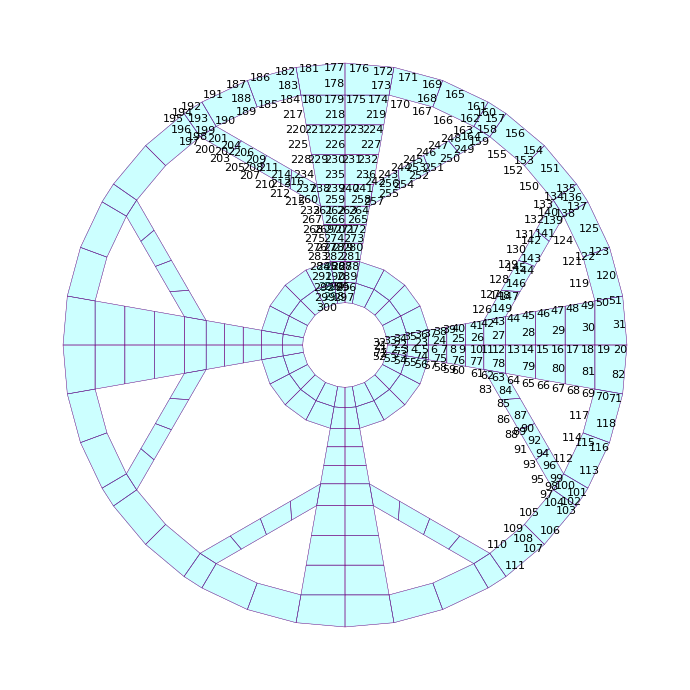

```mathematica
showMesh[gnum,gcoord,10,10,1500]
```

```mathematica
E0=75.0*10^9;
v=0.33;
ρ=2549.0;
gauss=gauss10;
```

```mathematica
AbsoluteTiming[{k,M,nu0}=mk0[E0,v,ρ,gauss,gcoord,gnum];]
```

{1448.91,Null}

```mathematica
Export["kmu_expel.mat",{"k0"->k,"m0"->M,"nu0"->nu0},"Version"->Automatic];
```